```mathematica
Needs["PlotLegends`"];

GetSeries[file_]:=Block[{line,points={},title},
title=Read[file,String];
line=Read[file,String];
While[line≠"END-SERIES",
AppendTo[points,ToExpression[RowBox[{"{",line,"}"}]]];
line=Read[file,String]
];
{title,points}
]

showplot[statsfile_]:=Block[
{file,title,dimensions,dimnames={},series={},numseries},
file = OpenRead[statsfile];
title = Read[file, String];
dimensions = Read[file, Real];
Do[AppendTo[dimnames, Read[file, String]],{dimensions}];
numseries= Read[file, Number];
Do[AppendTo[series,GetSeries[file]],{numseries}]
dimnames;
Close[file];
(*Print[series[[All,1]]]*)
If[dimensions==3,
(*Only one of these will be returned, depending on the number of dimensions*)
ListPlot3D[series[[All,2]], InterpolationOrder->3,AxesLabel -> dimnames,ColorFunction->"Rainbow",Mesh->None],
ListPlot[series[[All,2]],Joined->True, InterpolationOrder->1 ,AxesLabel -> dimnames,Mesh->None,PlotRange->{.2,.6},Filling->Axis,AxesOrigin->{0,0.25} ,PlotLegend-> series[[All,1]],LegendPosition->{0.6,-0.4}
]]
(*,PlotLegend-> series[[All,1]] *)
]

statsfile="C:\\cygwin\\home\\deco\\trunk\\GA_TestBench\\Data Files\\Really Nice Data\\HUGE-TYPE2 FullAverageStats(-1210014058) over 1 iterations with 35820 evals 120 pop 300 gens 1 copies 6 mutations 110 crossovers 3 randoms.txt";
s2="C:\\cygwin\\home\\deco\\trunk\\GA_TestBench\\Data Files\\Really Nice Data\\GA Parameters Data with 5 trials, population 101 and 200 generations.txt";

showplot[statsfile]
showplot[s2]
```

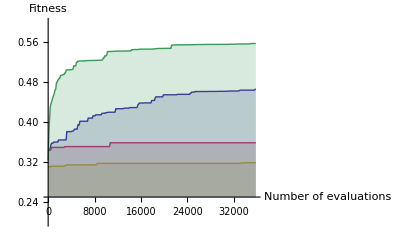

-Graphics3D-

Do::iterb: "
StyleBox[\"\\\"<Iterator >\\\"\", \"MT\"]
StyleBox[
RowBox[{\"{\", \"numseries\", \"}\"}], \"MT\"]
StyleBox[\"\\\"< does not have appropriate bounds.>\\\"\", \"MT\"] (*ButtonBox[

```mathematica
600^(7 8 43)//N
```

6.14060163373382×10^6689

```mathematica
FactorInteger@600
```

{{2,3},{3,1},{5,2}}